#### Radial propagator to fit Δ

```mathematica
geo=Import["/Users/hattrick/Desktop/Dean/AdS2-Lattice/phirad.dat",{"Data",All,1}];
phirad=Import["/Users/hattrick/Desktop/Dean/AdS2-Lattice/phirad.dat",{"Data",All,3}];
```

```mathematica
(* phirad is the radial propagator from the center to a point on the outer layer; geo is the geodesic distance between the center and said point *)
```

```mathematica
Log[ Exp[-Δ*σ]/(1-Exp[-2*σ])^Δ]//PowerExpand
```

-Δ σ-Δ Log[1-ⅇ^(-2 σ)]

```mathematica
(* this is the exact analytic expression for the propagator for d=1. If we plot phirad against this on a log-log plot, Δ will simply be the slope of the fitted line. *)
```

```mathematica
anaprop = Exp[-Δ*geo]/(1-Exp[-2*geo])^Δ;
```

```mathematica
data=Transpose[{-geo- Log[1-ⅇ^(-2*geo)],Log[phirad]}];
```

```mathematica
Transpose[{{1,2,3},{a,b,c}}]
```

{{1,a},{2,b},{3,c}}

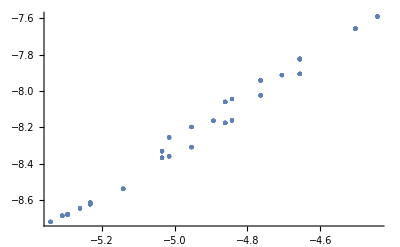

```mathematica
ListPlot[data]
```

```mathematica
Fit[data,{1,x},x]
```

-1.78275+1.30426 x

```mathematica
(* so Δ=1.30426 according to the fit *)
```

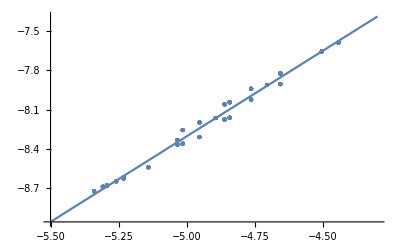

```mathematica
Show[{Plot[-1.7827453905442734+1.3042566811485976 x,{x,-5.5,-4.3}],ListPlot[data]},PlotRange->Full]
```

```mathematica
(* Δ*(Δ-1)==m^2 *)
```

```mathematica
Δ*(Δ-1)/.Δ->1.3042566811485976
```

0.396829

```mathematica
1/0.396828809172157
```

2.51998

```mathematica
(* so a^2 = 2.52 *)
```